# Spójniki ekstensjonalne

```mathematica
f=False; t=True;
boolPairs = {{f,f},{f,t},{t,f},{t,t}};
B1[x_,y_]:=Return[f];
B2[x_,y_]:=If[x==f,Return[f],Return[y]]; (*koniunkcja*)
B3[x_,y_]:=If[x==f,Return[f],Return[¬y]];
B4[x_,y_]:=Return[x];
B5[x_,y_]:=If[x==f,Return[y],Return[f]];
B6[x_,y_]:= Return[y];
B7[x_,y_]:=If[x==f,Return[y],Return[¬y]]; (*alternatywa wykluczająca*)
B8[x_,y_]:=If[x==f,Return[y],Return[t]]; (*alternatywa*)
B9[x_,y_]:=If[x==f,Return[¬y],Return[f]]; (*binegacja/strzałka Pierce'a*)
B10[x_,y_]:=If[x==f,Return[¬y],Return[y]]; (*równoważność*)
B11[x_,y_]:=Return[¬y];
B12[x_,y_]:=If[x==f,Return[¬y],Return[t]];
B13[x_,y_]:=Return[¬x];
B14[x_,y_]:=If[x==f,Return[t],Return[y]]; (*implikacja*)
B15[x_,y_]:=If[x==f,Return[t],Return[¬y]]; (*dysjunkcja/kreska Sheffera*)
B16[x_,y_]:=Return[t];
B = {B1,B2,B3,B4,B5,B6,B7,B8,B9,B10,B11,B12,B13,B14,B15,B16};
UzupelnijZbiorb[BSet_]:=Module[{array={},set},
Do[{
set={};
Do[AppendTo[set,funktor[pair[[1]],pair[[2]]]],{pair,boolPairs}];
AppendTo[array,set];},
{funktor,BSet}
];
Return[array]
];
b=UzupelnijZbiorb[B];
firstline={};
Module[{i},For[i=1,i≤16,i++,AppendTo[firstline,StringJoin[{"B",ToString[i]}]]]];
TablicaPrawdyB[B_]:=Module[{},TableForm[Boole[B],TableAlignments -> Center,TableDirections->Row,TableHeadings-> {firstline,{"(0, 0)","(0, 1)","(1, 0)","(1, 1)"}}]];
TablicaPrawdyB[b]
```

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
(0, 0) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
(0, 1) | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
(1, 0) | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
(1, 1) | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1

```mathematica
Func[f1_,f2_,f3_]:=Module[{set={},i},
	If[f2==0,
		If[f3==0,set=b[[f1]],
			{
			AppendTo[set,B[[f1]][f,b[[f3]][[1]]] ];AppendTo[set,B[[f1]][f,b[[f3]][[2]]] ];
			AppendTo[set,B[[f1]][t,b[[f3]][[3]]] ];AppendTo[set,B[[f1]][t,b[[f3]][[4]]] ];
			}
		],
		If[f3≠0,For[i=1,i≤4,i++,AppendTo[set,B[[f1]][b[[f2]][[i]],b[[f3]][[i]]] ] ],
			{
			AppendTo[set,B[[f1]][b[[f2]][[1]],f] ];AppendTo[set,B[[f1]][b[[f2]][[2]],t] ];
			AppendTo[set,B[[f1]][b[[f2]][[3]],f] ];AppendTo[set,B[[f1]][b[[f2]][[4]],t] ];
			}
		]
	];
	Return[set]
];
KtoryFunktorB[f1_,f2_,f3_]:=Module[{set=Func[f1,f2,f3]},For[i=1,i≤16,i++,If[set==b[[i]],Return[i]]]];
```

```mathematica
list3d={};
Module[{i,j,k,array,set},
	For[i=1,i≤16,i++,
	{
		array={};
		For[j=1,j≤16,j++,
			{
			set={};
			For[k=1,k≤16,k++,AppendTo[set,KtoryFunktorB[i,j,k]]];
			AppendTo[array,set];
			}
		];
		AppendTo[list3d,array];
	}
	]
];
Wypisz[funktor_]:= {Print[Style[StringJoin["B",ToString[funktor]],18,Red]];
Print[TableForm[list3d[[funktor]],TableAlignments->Center,TableHeadings->{firstline,firstline}]]};
```

Zdefiniujmy następujące złożenie funktorów dwuargumentowych:  B_i(B_1, B_2) :=  B_i( B_1(x,y), B_2(x,y) ).
Poszukajmy teraz takiej pary funktorów (B_1, B_2), która podstawiona jako argument do dowolnego spójnika B_i da w rezultacie właśnie ten spójnik.
Szukamy więc funktora o następującej własności:	   (xB_1y) B_i ( xB_2y) = (xB_iy).
Na podstawie tablic prawdy utworzonych dla takich złożeń łatwo udowodnić, że istnieje tylko jedna para spełniająca powyższą nierówność. Wystarczy spojrzeć na tablice dla B4 i B6:
	1. w tablicy dla B4 spójnik ten uzyskujemy tylko, gdy pierwszym argumentem jest B4 (drugi argument jest nieistotny);
	2. w tablicy dla B6 spójnik ten uzyskujemy tylko, gdy drugim argumentem jest B6 (pierwszy argument jest nieistotny).

```mathematica
Wypisz[4];Wypisz[6];
```

B4

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
B3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
B4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
B5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
B6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6
B7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7
B8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
B9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9
B10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
B11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11
B12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12
B13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13
B14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14
B15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15
B16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16

B6

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B3 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B4 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B5 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B6 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B7 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B9 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B10 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B11 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B12 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B13 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B14 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B15 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B16 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16

Stąd prosty wniosek, że naszym jedynym kandydatem na taką parę jest (B4,B6). Poniżej sprawdzimy, czy własność ta jest zachowana dla pozostałych funktorów.

```mathematica
Module[{set={}},
For[i=1, i≤16,i++, AppendTo[set, KtoryFunktorB[i,4,6]]];
Print[Style["Bi(B4,B6)",18,Red],"\n",TableForm[set, TableAlignments-> Center, TableDirections->Row, TableHeadings-> {firstline}]]
];
```

Bi(B4,B6)
B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16

Tworząc tablice prawdy dla dwóch zmiennych x i y, możemy te zmienne zastąpić kolejno wyrażeniami B4(x,y) i B6(x,y), gdyż ich wartości odpowiadają naszemu systemowi wartościowania. 

	Na podstawie tablic prawdy zdefiniowanego przez nas złożenia możemy udowodnić, że nie istnieją żadne inne niż dysjunkcja (B15) oraz binegacja (B9) dwuargumentowe ekstensjonalne spójniki zdaniotwórcze w pełni wystarczające do zdefiniowania innych spójników dwuargumentowych.
	Sprawdźmy to po kolei dla poszczególnych funktorów.

```mathematica
Wypisz[1];Wypisz[16];
```

B1

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B7 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B8 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B9 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B10 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B12 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B14 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B15 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B16 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

B16

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B2 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B3 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B4 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B5 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B6 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B7 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B8 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B9 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B10 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B11 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B12 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B13 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B14 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B15 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16

Jest to przykład trywialny - każde zdanie utworzone za pomocą spójnika B1 jest fałszywe, a za pomocą B16 - prawdziwe. Nie możemy więc za ich pomocą uzyskać żadnego innego spójnika.

```mathematica
Wypisz[2];
```

B2

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2
B3 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3
B4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4
B5 | 1 | 1 | 1 | 1 | 5 | 5 | 5 | 5 | 1 | 1 | 1 | 1 | 5 | 5 | 5 | 5
B6 | 1 | 2 | 1 | 2 | 5 | 6 | 5 | 6 | 1 | 2 | 1 | 2 | 5 | 6 | 5 | 6
B7 | 1 | 1 | 3 | 3 | 5 | 5 | 7 | 7 | 1 | 1 | 3 | 3 | 5 | 5 | 7 | 7
B8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
B9 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9
B10 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10
B11 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 9 | 9 | 11 | 11 | 9 | 9 | 11 | 11
B12 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12
B13 | 1 | 1 | 1 | 1 | 5 | 5 | 5 | 5 | 9 | 9 | 9 | 9 | 13 | 13 | 13 | 13
B14 | 1 | 2 | 1 | 2 | 5 | 6 | 5 | 6 | 9 | 10 | 9 | 10 | 13 | 14 | 13 | 14
B15 | 1 | 1 | 3 | 3 | 5 | 5 | 7 | 7 | 9 | 9 | 11 | 11 | 13 | 13 | 15 | 15
B16 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16

Funktor B16 możemy zdefiniować tylko za pomocą złożenia B2(B16,B16). Tak więc nie możemy go uzyskać posługując się jedynie funktorem B2.

```mathematica
Wypisz[8];
```

B8

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B2 | 2 | 2 | 4 | 4 | 6 | 6 | 8 | 8 | 10 | 10 | 12 | 12 | 14 | 14 | 16 | 16
B3 | 3 | 4 | 3 | 4 | 7 | 8 | 7 | 8 | 11 | 12 | 11 | 12 | 15 | 16 | 15 | 16
B4 | 4 | 4 | 4 | 4 | 8 | 8 | 8 | 8 | 12 | 12 | 12 | 12 | 16 | 16 | 16 | 16
B5 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16
B6 | 6 | 6 | 8 | 8 | 6 | 6 | 8 | 8 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16
B7 | 7 | 8 | 7 | 8 | 7 | 8 | 7 | 8 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16
B8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B9 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B10 | 10 | 10 | 12 | 12 | 14 | 14 | 16 | 16 | 10 | 10 | 12 | 12 | 14 | 14 | 16 | 16
B11 | 11 | 12 | 11 | 12 | 15 | 16 | 15 | 16 | 11 | 12 | 11 | 12 | 15 | 16 | 15 | 16
B12 | 12 | 12 | 12 | 12 | 16 | 16 | 16 | 16 | 12 | 12 | 12 | 12 | 16 | 16 | 16 | 16
B13 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16
B14 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16
B15 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16
B16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16

Sytuacja jak wyżej, tym razem nie jesteśmy w stanie uzyskać funktora B1.

```mathematica
Wypisz[3];
```

B3

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1
B3 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1
B4 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1
B5 | 5 | 5 | 5 | 5 | 1 | 1 | 1 | 1 | 5 | 5 | 5 | 5 | 1 | 1 | 1 | 1
B6 | 6 | 5 | 6 | 5 | 2 | 1 | 2 | 1 | 6 | 5 | 6 | 5 | 2 | 1 | 2 | 1
B7 | 7 | 7 | 5 | 5 | 3 | 3 | 1 | 1 | 7 | 7 | 5 | 5 | 3 | 3 | 1 | 1
B8 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B10 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1
B11 | 11 | 11 | 9 | 9 | 11 | 11 | 9 | 9 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1
B12 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 9 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1
B13 | 13 | 13 | 13 | 13 | 9 | 9 | 9 | 9 | 5 | 5 | 5 | 5 | 1 | 1 | 1 | 1
B14 | 14 | 13 | 14 | 13 | 10 | 9 | 10 | 9 | 6 | 5 | 6 | 5 | 2 | 1 | 2 | 1
B15 | 15 | 15 | 13 | 13 | 11 | 11 | 9 | 9 | 7 | 7 | 5 | 5 | 3 | 3 | 1 | 1
B16 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1

B16 odpowiada złożeniu B3(B16,B1), a więc jest zależny od samego siebie -- nie możemy go uzyskać za pomocą B3.

```mathematica
Wypisz[5];
```

B5

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B2 | 1 | 1 | 3 | 3 | 5 | 5 | 7 | 7 | 9 | 9 | 11 | 11 | 13 | 13 | 15 | 15
B3 | 1 | 2 | 1 | 2 | 5 | 6 | 5 | 6 | 9 | 10 | 9 | 10 | 13 | 14 | 13 | 14
B4 | 1 | 1 | 1 | 1 | 5 | 5 | 5 | 5 | 9 | 9 | 9 | 9 | 13 | 13 | 13 | 13
B5 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12
B6 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 9 | 9 | 11 | 11 | 9 | 9 | 11 | 11
B7 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10
B8 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9
B9 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
B10 | 1 | 1 | 3 | 3 | 5 | 5 | 7 | 7 | 1 | 1 | 3 | 3 | 5 | 5 | 7 | 7
B11 | 1 | 2 | 1 | 2 | 5 | 6 | 5 | 6 | 1 | 2 | 1 | 2 | 5 | 6 | 5 | 6
B12 | 1 | 1 | 1 | 1 | 5 | 5 | 5 | 5 | 1 | 1 | 1 | 1 | 5 | 5 | 5 | 5
B13 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4
B14 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3
B15 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2
B16 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

B16 odpowiada złożeniu B5(B1,B16), a więc jest zależny od samego siebie -- nie możemy go uzyskać za pomocą B5.

```mathematica
Wypisz[12];
```

B12

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B2 | 16 | 16 | 14 | 14 | 12 | 12 | 10 | 10 | 8 | 8 | 6 | 6 | 4 | 4 | 2 | 2
B3 | 16 | 15 | 16 | 15 | 12 | 11 | 12 | 11 | 8 | 7 | 8 | 7 | 4 | 3 | 4 | 3
B4 | 16 | 16 | 16 | 16 | 12 | 12 | 12 | 12 | 8 | 8 | 8 | 8 | 4 | 4 | 4 | 4
B5 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 13 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5
B6 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 8 | 8 | 6 | 6 | 8 | 8 | 6 | 6
B7 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 8 | 7 | 8 | 7 | 8 | 7 | 8 | 7
B8 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
B9 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9
B10 | 16 | 16 | 14 | 14 | 12 | 12 | 10 | 10 | 16 | 16 | 14 | 14 | 12 | 12 | 10 | 10
B11 | 16 | 15 | 16 | 15 | 12 | 11 | 12 | 11 | 16 | 15 | 16 | 15 | 12 | 11 | 12 | 11
B12 | 16 | 16 | 16 | 16 | 12 | 12 | 12 | 12 | 16 | 16 | 16 | 16 | 12 | 12 | 12 | 12
B13 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 13
B14 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14
B15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15
B16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16

B1 odpowiada złożeniu B12(B1,B16), a więc jest zależny od samego siebie -- nie możemy go uzyskać za pomocą B12.

```mathematica
Wypisz[14];
```

B14

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B2 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16
B3 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16
B4 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16
B5 | 12 | 12 | 12 | 12 | 16 | 16 | 16 | 16 | 12 | 12 | 12 | 12 | 16 | 16 | 16 | 16
B6 | 11 | 12 | 11 | 12 | 15 | 16 | 15 | 16 | 11 | 12 | 11 | 12 | 15 | 16 | 15 | 16
B7 | 10 | 10 | 12 | 12 | 14 | 14 | 16 | 16 | 10 | 10 | 12 | 12 | 14 | 14 | 16 | 16
B8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B10 | 7 | 8 | 7 | 8 | 7 | 8 | 7 | 8 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16
B11 | 6 | 6 | 8 | 8 | 6 | 6 | 8 | 8 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16
B12 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16
B13 | 4 | 4 | 4 | 4 | 8 | 8 | 8 | 8 | 12 | 12 | 12 | 12 | 16 | 16 | 16 | 16
B14 | 3 | 4 | 3 | 4 | 7 | 8 | 7 | 8 | 11 | 12 | 11 | 12 | 15 | 16 | 15 | 16
B15 | 2 | 2 | 4 | 4 | 6 | 6 | 8 | 8 | 10 | 10 | 12 | 12 | 14 | 14 | 16 | 16
B16 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16

B1 odpowiada złożeniu B14(B16,B1), a więc jest zależny od samego siebie -- nie możemy go uzyskać za pomocą B14.

```mathematica
Wypisz[4];
```

B4

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
B3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
B4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
B5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
B6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6
B7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7
B8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
B9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9
B10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
B11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11
B12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12
B13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13
B14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14
B15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15
B16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16

i-ty spójnik odpowiada złożeniu siebie samego z dowolnym innym spójnikiem, a więc jest od siebie zależny.

```mathematica
Wypisz[6];
```

B6

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B3 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B4 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B5 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B6 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B7 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B9 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B10 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B11 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B12 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B13 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B14 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B15 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B16 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16

i-ty spójnik odpowiada złożeniu dowolnego spójnika z sobą samym, a więc jest od siebie zależny.

```mathematica
Wypisz[11];
```

B11

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B2 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B3 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B4 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B5 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B6 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B7 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B8 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B9 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B10 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B11 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B12 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B13 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B14 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B15 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B16 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1

B16 uzyskamy ze złożenia dowolnego spójnika z B1, zaś B1 uzyskamy ze złożenia dowolnego spójnika z B16.
W efekcie spójniki B16 są zależne od siebie nawzajem B1, a więc są też zależne od siebie samych.

```mathematica
Wypisz[13];
```

B13

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B2 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15
B3 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14
B4 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13
B5 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12
B6 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11
B7 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
B8 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9
B9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
B10 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7
B11 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6
B12 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
B13 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
B14 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
B15 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
B16 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

B16 uzyskamy ze złożenia B1 z dowolnym spójnikiem, zaś B1 uzyskamy ze złożenia B16 z dowolnych spójnikiem.
W efekcie funktory B16 są zależne od siebie nawzajem B1, a więc są też zależne od siebie samych.

Dla spójników B7, B9, B10 i B15 trzeba rozpatrzyć więcej przypadków. Rozważając przypadki dla każdego z tych funktorów, jako argumenty możemy podstawiać tylko dany funktor oraz funktory B4 i B6 odpowiadające możliwym wartościowaniom dwóch zmiennych zdaniowych.

```mathematica
WypiszDlaKilku[argumenty_,funktor_]:=Module[{tablicaB={},tablica ,heading={}},
Do[ {tablica={};
     Do[AppendTo[tablica,KtoryFunktorB[funktor,n,m]],{m,argumenty}];
     AppendTo[tablicaB, tablica];
     AppendTo[heading,StringJoin["B",ToString[n]]]},{n,argumenty}];
	Return[TableForm[tablicaB,TableAlignments->Center,TableHeadings->{heading,heading}]];
];
```

```mathematica
Wypisz[7];Print["\n"];
{
	Labeled[WypiszDlaKilku[{4,6,7},7],Style[StringJoin["B",ToString[7]],15,Purple]],
"\t"Labeled[WypiszDlaKilku[{1,4,6,7},7],Style[StringJoin["B",ToString[7]],15,Purple]],
"\t"Labeled[WypiszDlaKilku[{1,4,6,7},1],Style[StringJoin["B",ToString[1]],15,Orange]],
"\t"Labeled[WypiszDlaKilku[{1,4,6,7},4],Style[StringJoin["B",ToString[4]],15,Green]],
"\t"Labeled[WypiszDlaKilku[{1,4,6,7},6],Style[StringJoin["B",ToString[6]],15,Blue]]
}
```

B7

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B2 | 2 | 1 | 4 | 3 | 6 | 5 | 8 | 7 | 10 | 9 | 12 | 11 | 14 | 13 | 16 | 15
B3 | 3 | 4 | 1 | 2 | 7 | 8 | 5 | 6 | 11 | 12 | 9 | 10 | 15 | 16 | 13 | 14
B4 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 12 | 11 | 10 | 9 | 16 | 15 | 14 | 13
B5 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 13 | 14 | 15 | 16 | 9 | 10 | 11 | 12
B6 | 6 | 5 | 8 | 7 | 2 | 1 | 4 | 3 | 14 | 13 | 16 | 15 | 10 | 9 | 12 | 11
B7 | 7 | 8 | 5 | 6 | 3 | 4 | 1 | 2 | 15 | 16 | 13 | 14 | 11 | 12 | 9 | 10
B8 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9
B9 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
B10 | 10 | 9 | 12 | 11 | 14 | 13 | 16 | 15 | 2 | 1 | 4 | 3 | 6 | 5 | 8 | 7
B11 | 11 | 12 | 9 | 10 | 15 | 16 | 13 | 14 | 3 | 4 | 1 | 2 | 7 | 8 | 5 | 6
B12 | 12 | 11 | 10 | 9 | 16 | 15 | 14 | 13 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5
B13 | 13 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4
B14 | 14 | 13 | 16 | 15 | 10 | 9 | 12 | 11 | 6 | 5 | 8 | 7 | 2 | 1 | 4 | 3
B15 | 15 | 16 | 13 | 14 | 11 | 12 | 9 | 10 | 7 | 8 | 5 | 6 | 3 | 4 | 1 | 2
B16 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1

{ | B4 | B6 | B7
B4 | 1 | 7 | 6
B6 | 7 | 1 | 4
B7 | 6 | 4 | 1B7,	  | B1 | B4 | B6 | B7
B1 | 1 | 4 | 6 | 7
B4 | 4 | 1 | 7 | 6
B6 | 6 | 7 | 1 | 4
B7 | 7 | 6 | 4 | 1B7,	  | B1 | B4 | B6 | B7
B1 | 1 | 1 | 1 | 1
B4 | 1 | 1 | 1 | 1
B6 | 1 | 1 | 1 | 1
B7 | 1 | 1 | 1 | 1B1,	  | B1 | B4 | B6 | B7
B1 | 1 | 1 | 1 | 1
B4 | 4 | 4 | 4 | 4
B6 | 6 | 6 | 6 | 6
B7 | 7 | 7 | 7 | 7B4,	  | B1 | B4 | B6 | B7
B1 | 1 | 4 | 6 | 7
B4 | 1 | 4 | 6 | 7
B6 | 1 | 4 | 6 | 7
B7 | 1 | 4 | 6 | 7B6}

Na początku rozpatrujemy dostępne wartości B7 dla argumentów B4, B6 i B7. Jak widzimy, jesteśmy w stanie uzyskać kolejny funktor - B1. Rozszerzamy więc naszą tabelę o kolejne wartości.
Widzimy, że nie jesteśmy w stanie w ten sposób uzyskać innych spójników niż B1, B4, B6 i B7. Możemy jednak użyć ich jako argumentów w odpowiadających im funkcjach, co obrazują 3 ostatnie tabele.
Pomimo tego zabiegu, jesteśmy w stanie utworzyć tylko 4 funktory za pomocą B7.

```mathematica
Wypisz[10];Print["\n"];{Labeled[WypiszDlaKilku[{4,6,10},10],Style[StringJoin["B",ToString[10]],15,Purple]], "\t"Labeled[WypiszDlaKilku[{4,6,10,16},10],Style[StringJoin["B",ToString[10]],15,Purple]], "\t"Labeled[WypiszDlaKilku[{4,6,10,16},4],Style[StringJoin["B",ToString[4]],15,Orange]],"\t"Labeled[WypiszDlaKilku[{4,6,10,16},6],Style[StringJoin["B",ToString[6]],15,Green]],"\t"Labeled[WypiszDlaKilku[{4,6,10,16},16],Style[StringJoin["B",ToString[16]],15,Blue]]}
```

B10

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B2 | 15 | 16 | 13 | 14 | 11 | 12 | 9 | 10 | 7 | 8 | 5 | 6 | 3 | 4 | 1 | 2
B3 | 14 | 13 | 16 | 15 | 10 | 9 | 12 | 11 | 6 | 5 | 8 | 7 | 2 | 1 | 4 | 3
B4 | 13 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4
B5 | 12 | 11 | 10 | 9 | 16 | 15 | 14 | 13 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5
B6 | 11 | 12 | 9 | 10 | 15 | 16 | 13 | 14 | 3 | 4 | 1 | 2 | 7 | 8 | 5 | 6
B7 | 10 | 9 | 12 | 11 | 14 | 13 | 16 | 15 | 2 | 1 | 4 | 3 | 6 | 5 | 8 | 7
B8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
B9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9
B10 | 7 | 8 | 5 | 6 | 3 | 4 | 1 | 2 | 15 | 16 | 13 | 14 | 11 | 12 | 9 | 10
B11 | 6 | 5 | 8 | 7 | 2 | 1 | 4 | 3 | 14 | 13 | 16 | 15 | 10 | 9 | 12 | 11
B12 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 13 | 14 | 15 | 16 | 9 | 10 | 11 | 12
B13 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 12 | 11 | 10 | 9 | 16 | 15 | 14 | 13
B14 | 3 | 4 | 1 | 2 | 7 | 8 | 5 | 6 | 11 | 12 | 9 | 10 | 15 | 16 | 13 | 14
B15 | 2 | 1 | 4 | 3 | 6 | 5 | 8 | 7 | 10 | 9 | 12 | 11 | 14 | 13 | 16 | 15
B16 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16

{ | B4 | B6 | B10
B4 | 16 | 10 | 6
B6 | 10 | 16 | 4
B10 | 6 | 4 | 16B10,	  | B4 | B6 | B10 | B16
B4 | 16 | 10 | 6 | 4
B6 | 10 | 16 | 4 | 6
B10 | 6 | 4 | 16 | 10
B16 | 4 | 6 | 10 | 16B10,	  | B4 | B6 | B10 | B16
B4 | 4 | 4 | 4 | 4
B6 | 6 | 6 | 6 | 6
B10 | 10 | 10 | 10 | 10
B16 | 16 | 16 | 16 | 16B4,	  | B4 | B6 | B10 | B16
B4 | 4 | 6 | 10 | 16
B6 | 4 | 6 | 10 | 16
B10 | 4 | 6 | 10 | 16
B16 | 4 | 6 | 10 | 16B6,	  | B4 | B6 | B10 | B16
B4 | 16 | 16 | 16 | 16
B6 | 16 | 16 | 16 | 16
B10 | 16 | 16 | 16 | 16
B16 | 16 | 16 | 16 | 16B16}

Sytuacja podobna jak dla funktora B7.

```mathematica
Wypisz[9];
Module[{headings={"(4,4)","(6,6)","(9,9)","(13,13)","(11,11)","(8,8)","(4,9)","(5,5)","(6,9)","(3,3)","(3,5)","(10,10)","(3,13)","(2,2)","(8,11)","(1,1)"},values={13,11,8,4,6,9,5,12,3,14,10,7,2,15,1,16}},Print["\n",Style["B9",15,Purple],"\n",TableForm[values, TableAlignments-> Right, TableDirections->Row, TableHeadings-> {headings}]]
];
```

B9

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B2 | 15 | 15 | 13 | 13 | 11 | 11 | 9 | 9 | 7 | 7 | 5 | 5 | 3 | 3 | 1 | 1
B3 | 14 | 13 | 14 | 13 | 10 | 9 | 10 | 9 | 6 | 5 | 6 | 5 | 2 | 1 | 2 | 1
B4 | 13 | 13 | 13 | 13 | 9 | 9 | 9 | 9 | 5 | 5 | 5 | 5 | 1 | 1 | 1 | 1
B5 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 9 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1
B6 | 11 | 11 | 9 | 9 | 11 | 11 | 9 | 9 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1
B7 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1
B8 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
B9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
B10 | 7 | 7 | 5 | 5 | 3 | 3 | 1 | 1 | 7 | 7 | 5 | 5 | 3 | 3 | 1 | 1
B11 | 6 | 5 | 6 | 5 | 2 | 1 | 2 | 1 | 6 | 5 | 6 | 5 | 2 | 1 | 2 | 1
B12 | 5 | 5 | 5 | 5 | 1 | 1 | 1 | 1 | 5 | 5 | 5 | 5 | 1 | 1 | 1 | 1
B13 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1
B14 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1
B15 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1
B16 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

B9
(4,4) | (6,6) | (9,9) | (13,13) | (11,11) | (8,8) | (4,9) | (5,5) | (6,9) | (3,3) | (3,5) | (10,10) | (3,13) | (2,2) | (8,11) | (1,1)
13 | 11 | 8 | 4 | 6 | 9 | 5 | 12 | 3 | 14 | 10 | 7 | 2 | 15 | 1 | 16

Powyższa tabela przedstawia jak możemy uzyskać kolejne funktory zdaniotwórcze za pomocą B9. Jako argumentów w kolejnych kolumnach używamy tylko spójników, które otrzymaliśmy w kolumnach wcześniejszych.

```mathematica
Wypisz[15];
Module[{headings={"(4,4)","(6,6)","(15,15)","(13,13)","(11,11)","(2,2)","(4,15)","(12,12)","(15,4)","(14,14)","(2,3)","(16,16)","(11,13)","(8,8)","(12,14)","(7,7)"},values={13,11,2,4,6,15,12,5,14,3,16,1,8,9,7,10}},Print["\n",Style["B15",15,Purple],"\n",TableForm[values, TableAlignments-> Center, TableDirections->Row, TableHeadings-> {headings}]]
];
```

B15

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
B1 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
B2 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15
B3 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14
B4 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 13
B5 | 16 | 16 | 16 | 16 | 12 | 12 | 12 | 12 | 16 | 16 | 16 | 16 | 12 | 12 | 12 | 12
B6 | 16 | 15 | 16 | 15 | 12 | 11 | 12 | 11 | 16 | 15 | 16 | 15 | 12 | 11 | 12 | 11
B7 | 16 | 16 | 14 | 14 | 12 | 12 | 10 | 10 | 16 | 16 | 14 | 14 | 12 | 12 | 10 | 10
B8 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9
B9 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
B10 | 16 | 15 | 16 | 15 | 16 | 15 | 16 | 15 | 8 | 7 | 8 | 7 | 8 | 7 | 8 | 7
B11 | 16 | 16 | 14 | 14 | 16 | 16 | 14 | 14 | 8 | 8 | 6 | 6 | 8 | 8 | 6 | 6
B12 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 13 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5
B13 | 16 | 16 | 16 | 16 | 12 | 12 | 12 | 12 | 8 | 8 | 8 | 8 | 4 | 4 | 4 | 4
B14 | 16 | 15 | 16 | 15 | 12 | 11 | 12 | 11 | 8 | 7 | 8 | 7 | 4 | 3 | 4 | 3
B15 | 16 | 16 | 14 | 14 | 12 | 12 | 10 | 10 | 8 | 8 | 6 | 6 | 4 | 4 | 2 | 2
B16 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1

B15
(4,4) | (6,6) | (15,15) | (13,13) | (11,11) | (2,2) | (4,15) | (12,12) | (15,4) | (14,14) | (2,3) | (16,16) | (11,13) | (8,8) | (12,14) | (7,7)
13 | 11 | 2 | 4 | 6 | 15 | 12 | 5 | 14 | 3 | 16 | 1 | 8 | 9 | 7 | 10

Sytuacja jak w B9.

Wniosek:
	Tylko funktory B9 (binegacja/strzałka Pierce’a) i B15 (dysjunkcja/kreska Sheffera) mogą samodzielnie definiować inne dwuargumentowe funktory zdaniotwórcze.

```mathematica
fraktale= {2,3,5,8,9,12,14,15};
calaPrzestrzen = {4,7,10,13};
prosta = {1,6,11,16};
list3dfrac={};Do[AppendTo[list3dfrac, list3d[[i]]],{i,fraktale}];
list3dline = {}; Do[AppendTo[list3dline, list3d[[i]]],{i,prosta}];
list3dsurface = {}; Do[AppendTo[list3dsurface, list3d[[i]]],{i,calaPrzestrzen}];
```

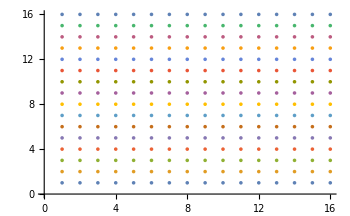
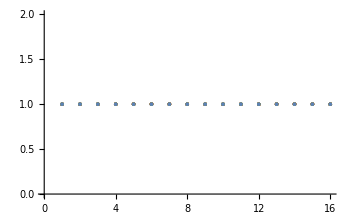
{-Graphics-B4 (B13,B7,B10),-Graphics-B1 (B16)}

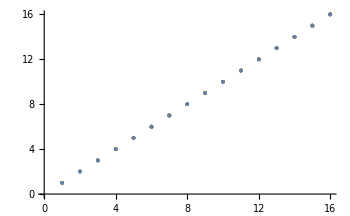
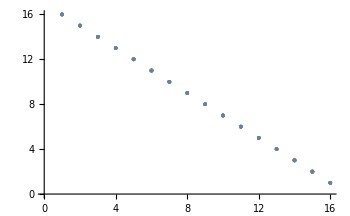
{-Graphics-B6,-Graphics-B11}

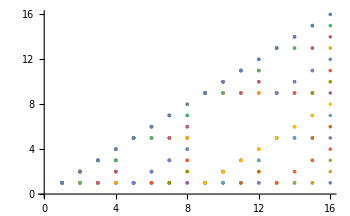
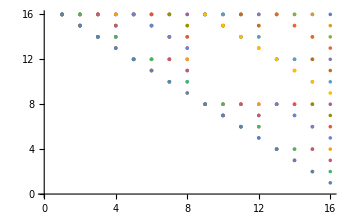
{-Graphics-B2 (B5),-Graphics-B15 (B12)}

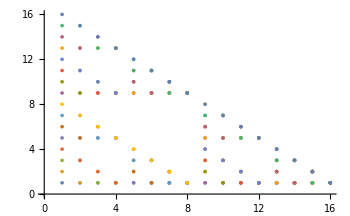
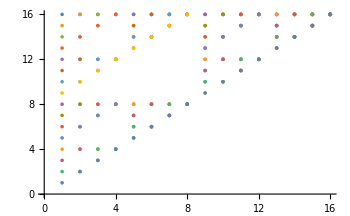
{-Graphics-B3 (B9),-Graphics-B14 (B8)}

```mathematica
{Labeled[ListPlot[list3d[[4]], ImageSize->350],"B4 (B13,B7,B10)"],Labeled[ListPlot[ list3d[[1]],ImageSize->350],"B1 (B16)"]}
{Labeled[ListPlot[list3d[[6]], ImageSize->350],"B6"],Labeled[ListPlot[list3d[[11]], ImageSize->350],"B11"]}
{Labeled[ListPlot[list3d[[2]], ImageSize->350],"B2 (B5)"], Labeled[ListPlot[list3d[[15]], ImageSize->350],"B15 (B12)"]}
{Labeled[ListPlot[list3d[[3]], ImageSize->350],"B3 (B9)"],Labeled[ListPlot[list3d[[14]], ImageSize->350],"B14 (B8)"]}
```

```mathematica
{ListPlot3D[list3d, PlotLegends->Range[16]], ListPlot3D[list3dfrac, PlotLegends-> fraktale], ListPlot3D[list3dline, PlotLegends->prosta],ListPlot3D[list3dsurface,PlotLegends-> calaPrzestrzen]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{ListPlot3D[{list3d[[1]],list3d[[16]]},PlotLegends->{1,16}],ListPlot3D[{list3d[[7]],list3d[[10]]},PlotLegends->{7,10}],ListPlot3D[{list3d[[4]],list3d[[13]]},PlotLegends->{4,13}],ListPlot3D[{list3d[[6]],list3d[[11]]},PlotLegends->{6,11}]}
{ListPlot3D[{list3d[[2]],list3d[[15]]},PlotLegends->{2,15}],ListPlot3D[{list3d[[8]],list3d[[9]]},PlotLegends->{8,9}],ListPlot3D[{list3d[[3]],list3d[[14]]},PlotLegends->{3,14}],ListPlot3D[{list3d[[5]],list3d[[12]]},PlotLegends->{5,12}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Module[{sX={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},dzialanie,grupy={}, wlasnosci={}},
Do[{
dzialanie= NewOpFSet[FSet@@sX, list3d[[f]]];
AppendTo[wlasnosci, {IsAssociative[dzialanie],HasNeutral[dzialanie],HasInverses[dzialanie],IsAbelian[dzialanie]}];
If[IsGroup[dzialanie],AppendTo[grupy,f]];
},{f,sX}];
TableForm[wlasnosci, TableAlignments->Center,TableDirections->Row, TableHeadings->{firstline,{"Laczne","El. neutralny", "El. odwrotny", "Przemienne"}}]
(*dD7 = NewOpFSet[sX, list3d[[7]]];
OpFSetTable[dD7];*)
]
```

| B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 | B16
Laczne | True | True | False | True | False | True | True | True | False | True | False | False | False | False | False | True
El. neutralny | False | True | False | False | False | False | True | True | False | True | False | False | False | False | False | False
El. odwrotny | False | False | False | False | False | False | True | False | False | True | False | False | False | False | False | False
Przemienne | True | True | False | False | False | False | True | True | True | True | False | False | False | False | True | True

```mathematica
dD7=  NewOpFSet[FSet[1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16], list3d[[7]]];
dD10=  NewOpFSet[FSet[1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16], list3d[[10]]];
{GetNeutral[dD7],GetNeutral[dD10]}
Module[{inverse7={},inverse10={}},
Do[{AppendTo[inverse7,GetInverse[dD7,i]];AppendTo[inverse10,GetInverse[dD10,i]]},{i,16}];Print["B7: ",inverse7, "\nB10: ", inverse10]]
```

{1,16}

B7: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}
B10: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}